## Shell - Model potentials

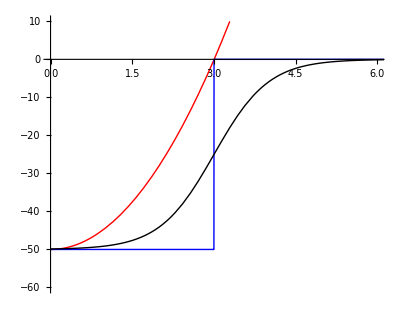

```mathematica
m=1;
ω=3.33;
V01=50;
V02=50;
V03=50;
a=0.5;
R0=3;
sho[r_]:=-V01+1/2 m*(ω*r)^2;
well[r_]:=Piecewise[{{-V02, r<=R0&& r>=-R0}, {0, r>R0 && r<-R0}}];
R=1.2;
vws[r_]:=-V03/(1+Exp[(Abs[r]-R0)/a]);
Plot[{sho[r],well[r],vws[r]},{r,0,7},AspectRatio->0.8,Axes->{True,True},Frame->False,FrameLabel->{"r [fm]","V(r) [MeV]"},PlotStyle->{{Red,Thick},{Blue,Thick},{Black,Thick}},PlotRange->{{0,6},{-60,10}},Ticks->None,AxesStyle->{ Directive[Arrowheads[{0,0.06}],Black,Thick,17,FontFamily->"Times",Bold],Directive[Arrowheads[{-0.06,0}],Black,Thick,17,FontFamily->"Times",Bold,AxesLabel->{"x","y"}]},PlotRange->{{0,9},{0,-65}}]
```